```mathematica
norm2D[{x_,y_}]:={-y,x}/√(x*x+y*y);
```

```mathematica
getCoefficient[Q_,N_]:=Module[
	{D,a,b,c},
	D=Length[Q];
	a=Table[P[N,m]×P[N,n],{m,D},{n,D}];
	c=N.Q;
	b=Table[P[N,m]×c,{m,D}];
	c=c×c;
	{a,b,c}
];
```

```mathematica
preSimplify2D[E_,l_]:=Flatten[P[Reap[Do[Scan[Sow[i,#]&,P[E,i]],{i,Length[E]}],Range[l]],2],1];
```

```mathematica
(* {i,{a,b,c},{p,e}} *)
simplify2D[curve_,num_]:=Module[
	{V,E,MV,ME,l,R,D,tc,ic,ik,id,tl,il,tn,in},
	{V,E}=curve;
	MV=Table[1,Length[V]];
	ME=Table[1,Length[E]];
	l=Length[V]-num;
	R=preSimplify2D[E,Length[V]];
	D=Table[{0,0,0},Length[E]];
	Do[
		D[[i,1]]=i;
		D[[i,2]]=getCoefficient[P[V,P[E,{i,1}]],norm2D[P[V,P[E,{i,1}]]-P[V,P[E,{i,2}]]]],
	{i,Length[E]}];
	Do[
		D[[i,3]]=getMinimizerQEM[Total[D[[Union@@R[[P[E,i]]],2]]]],
	{i,Length[E]}];
	
	Do[
		tc=P[MinimalBy[D,(If[P[ME,P[#,1]]==1,P[#,{3,2}],Infinity])&],1];
		ic=P[tc,1];
		ik=P[E,{ic,1}];
		id=P[E,{ic,2}];
		ME[[ic]]=0;
		MV[[id]]=0;
		V[[ik]]=P[tc,{3,1}];
		{tl,tn}=R[[P[E,ic]]];
		il=If[P[tl,1]==ic,P[tl,2],P[tl,1]];
		in=If[P[tn,1]==ic,P[tn,2],P[tn,1]];
		R[[ik]]={il,in};
		If[P[E,{in,1}]==id,E[[in,1]]=ik,E[[in,2]]=ik];
		D[[il,2]]=getCoefficient[P[V,ik],norm2D[P[V,P[E,{il,1}]]-P[V,P[E,{il,2}]]]];
		D[[in,2]]=getCoefficient[P[V,ik],norm2D[P[V,P[E,{in,1}]]-P[V,P[E,{in,2}]]]];
		D[[il,3]]=getMinimizerQEM[Total[D[[Union@@R[[P[E,il]]],2]]]];
		D[[in,3]]=getMinimizerQEM[Total[D[[Union@@R[[P[E,in]]],2]]]];,
	l];	

	
	V=P[Reap[Do[If[P[MV,i]==1,Sow[P[V,i]]],{i,Length[V]}]],{2,1}];
	l=1;
	Do[If[P[MV,i]==1,MV[[i]]=l++],{i,Length[MV]}];
	E=P[Reap[Do[If[P[ME,i]≠0,Sow[MV[[P[E,i]]]]],{i,Length[E]}]],{2,1}];
	{V,E}
];
```

```mathematica
(* Circle *)
numPoints=100;
circle={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]},{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
```

```mathematica
simplify2D[circle,5]
```

{0,0,1,0,2,3,0,4,0,5}

{{1,2},{10,3},{3,4},{3,5},{5,6},{6,7},{6,8},{8,9},{8,10},{10,1}}

{0,1,0,1,1,0,1,0,1,0}

{{{-0.633831,0.872393},{-1.,0.},{-0.633831,-0.872393},{0.633831,-0.872393},{0.983551,0.67704}},{{5,1},{1,2},{2,3},{3,4},{4,5}}}

```mathematica
showCurveWithPoints[{V_,E_},col_]:=Graphics[{{col,{Map[Line[V⟦#⟧]&,E]}},Map[Point,V]},Frame->False];
```

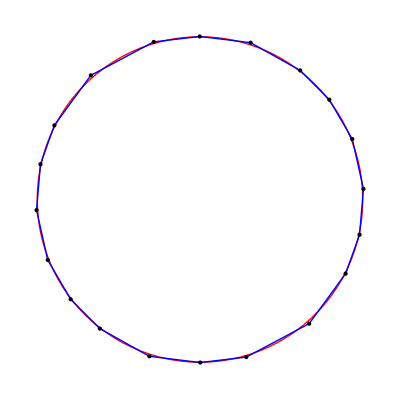

```mathematica
Show[showCurve[circle,RGBColor[1,0,0]],showCurveWithPoints[simplify2D[circle,20],RGBColor[0,0,1]]]
```

```mathematica
(* Wavy circle *)
numPoints=100;
circleWave={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]}*(1+.2*Sin[10π/numPoints*i]),{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
```

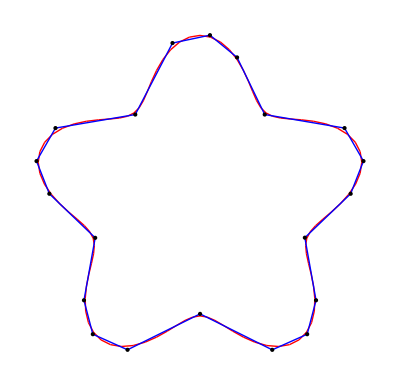

```mathematica
Show[showCurve[circleWave,RGBColor[1,0,0]],showCurveWithPoints[simplify2D[circleWave,20],RGBColor[0,0,1]]]
```

824

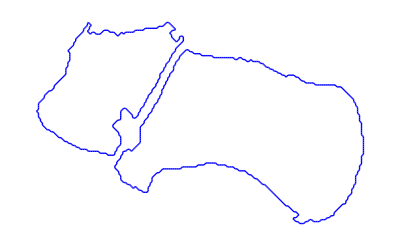

```mathematica
(* Bone *)
bone=Get["M4/dat/bone_2D.txt"];
Length[P[bone,1]]
showCurve[bone]
```

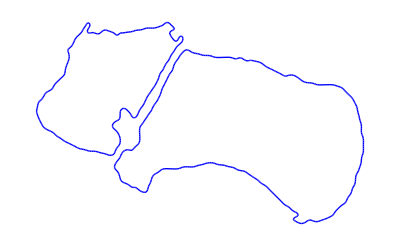

```mathematica
bonefair=fair[bone,20];
showCurve[bonefair]
```

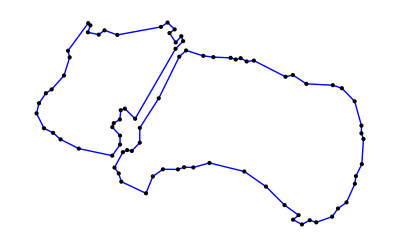

```mathematica
bonesim=simplify2D[bonefair,82];
showCurveWithPoints[bonesim,RGBColor[0,0,1]]
```